```mathematica
g[x_]:=-E^x
```

```mathematica
g'[x]
```

-ⅇ^x

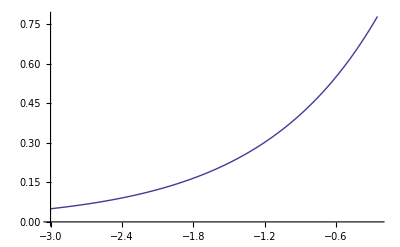

```mathematica
Plot[Abs[g'[x]],{x,-3,-0.25}]
```

```mathematica
q=0.8
```

0.8

```mathematica
x0=-1.7
Do[x=g[x0];ss=q/(1-q)Abs[x-x0];x0=x;Print[{x,ss}]
,{3}]
```

-1.7

{-0.182684,6.06927}

{-0.833032,2.60139}

{-0.434729,1.59321}